```mathematica
Integrate[1/(x^3+1),{x,0,1}]
```

1/18 (2 √3 π+Log[64])

```mathematica
Integrate[1/(1-x^2)^(1/2),{x,0,1}]
```

π/2

```mathematica
NIntegrate[e^x/(1+x^2)^(1/2),{x,0,1}]
```

NIntegrate::inumr: The integrand e^x/√1 + x^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{0, 1}}.

NIntegrate[e^x/(√(1+x^2)),{x,0,1}]

```mathematica
Integrate[e^x/(1+x^2)^(1/2),{x,0,-∞}]
```

∫_0^(-∞) e^x/(√(1+x^2))ⅆx

```mathematica
NIntegrate[Exp[x]/Sqrt[x^2+1],{x,0,1},AccuracyGoal->8]-exact
```

1.46897-exact

```mathematica
NIntegrate[2*Exp[x]/Sqrt[x^2+1],{x,0,-∞},AccuracyGoal->8]-exact
```

-1.50922-exact

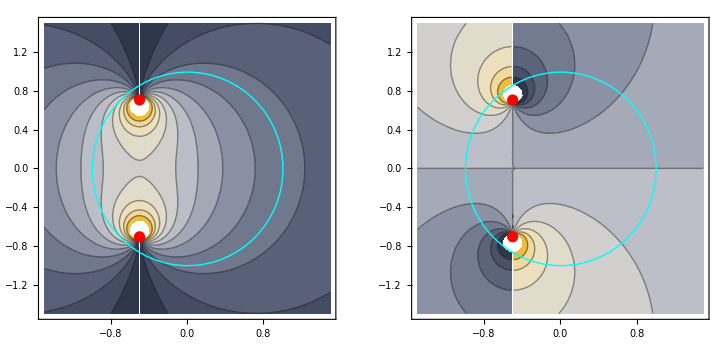

```mathematica
With[{z1=1/2 (-1-I Sqrt[2]),z2=1/2 (-1+I Sqrt[2])},GraphicsRow[Table[ContourPlot[g[1/Sqrt[4 (x+I y-z1) (x+I y-z2)]],{x,-1.5,1.5},{y,-1.5,1.5},ColorFunction->"GrayYellowTones",Epilog->{Cyan,Thick,Circle[{0,0}],Red,PointSize[0.02],Point[{Re@#,Im@#}&/@{z1,z2}]},Contours->11],{g,{Re,Im}}]]]
```